# Лаба 1

1) Раскрыть скобки в выражениях

```mathematica
Expand[(x-2)^4]
```

16-32 x+24 x^2-8 x^3+x^4

```mathematica
Expand[(x+Cos[x]-Sin[x])^4]
```

x^4+4 x^3 Cos[x]+6 x^2 Cos[x]^2+4 x Cos[x]^3+Cos[x]^4-4 x^3 Sin[x]-12 x^2 Cos[x] Sin[x]-12 x Cos[x]^2 Sin[x]-4 Cos[x]^3 Sin[x]+6 x^2 Sin[x]^2+12 x Cos[x] Sin[x]^2+6 Cos[x]^2 Sin[x]^2-4 x Sin[x]^3-4 Cos[x] Sin[x]^3+Sin[x]^4

2) Раскрыть скобки, результат сгруппировать по степеням a

```mathematica
Collect[Expand[((x+a)^2 + y)^3],a]
```

a^6+6 a^5 x+x^6+3 x^4 y+3 x^2 y^2+y^3+a^4 (15 x^2+3 y)+a^3 (20 x^3+12 x y)+a^2 (15 x^4+18 x^2 y+3 y^2)+a (6 x^5+12 x^3 y+6 x y^2)

3) Разложить на множители

```mathematica
Factor[(x^2+2 x+1) a^3+(3 y x^3+6 y x+3y)a^3+(3 y^2 x^3+6 y^2 x+3 y^2) a+x^2 y^3+2 x y^3+y^3]
```

a^3+2 a^3 x+a^3 x^2+3 a^3 y+6 a^3 x y+3 a^3 x^3 y+3 a y^2+6 a x y^2+3 a x^3 y^2+y^3+2 x y^3+x^2 y^3

4) Упростить выражения

```mathematica
Factor[Cos[x]^4+Sin[x]^4-6 Sin[x]^2 Cos[x]^2,Trig->True]
```

Cos[4 x]

```mathematica
Simplify[(Cos[y]^4+2 Sin[y] Cos[y]^3+Sin[y]^4-2 Cos[y]^2Sin[y]^2-2 Cos[y] Sin[y]^3)/(Cos[y]^2-Sin[y]^2)-2 Cos[y] Sin[y]]
```

Cos[2 y]

5) Найти пределы

```mathematica
Limit[(1+x)^(1/x),x->0]
```

ⅇ

```mathematica
Limit[Sin[x]/x,x->0]
```

1

```mathematica
Limit[(1+1/x)^x,x->Infinity]
```

ⅇ

```mathematica
Limit[(a^x-1)/x,x->0]
```

Log[a]

```mathematica
Limit[Exp[a Sin[x]], x -> Infinity]
```

ⅇ^(a Interval[{-1,1}])

```mathematica
Limit[1/x, x->-Infinity]
```

0

Вычислить производные

```mathematica
D[Sin[x],x]
```

Cos[x]

```mathematica
D[f[g[x]],x]
```

f'[g[x]] g'[x]

```mathematica
D[Sin[x y],{x,2},y]
```

-x y^2 Cos[x y]-2 y Sin[x y]

```mathematica
D[Log[(x-3)/(x+3)],{x,2}]
```

((3+x) ((2 (-3+x))/(3+x)^3-2/(3+x)^2))/(-3+x)+(-(-3+x)/(3+x)^2+1/(3+x))/(-3+x)-((3+x) (-(-3+x)/(3+x)^2+1/(3+x)))/(-3+x)^2

Найти интегралы

```mathematica
Integrate[x^2/(x+a)^3,x]
```

(a (3 a+4 x))/(2 (a+x)^2)+Log[a+x]

```mathematica
Integrate[x^2/Sqrt[a x+b],x]
```

(2 √(b+a x) (8 b^2-4 a b x+3 a^2 x^2))/(15 a^3)

```mathematica
Integrate[Sin[a x]/x,{x,-Infinity,Infinity}]
```

ConditionalExpression[π Sign[a], a∈ℝ]

```mathematica
Integrate[x Exp[a x] Sin[b x],x]
```

(ⅇ^(a x) (-b (-2 a+a^2 x+b^2 x) Cos[b x]+(-a^2+b^2+a^3 x+a b^2 x) Sin[b x]))/((a^2+b^2)^2)

```mathematica
Integrate[(x Sin[a x])/(x^2+b^2),{x, -Infinity, Infinity}]
```

ConditionalExpression[(a ⅇ^(-Abs[a]/(√(1/b^2))) π)/Abs[a], a∈ℝ&&(Re[b^2]≥0||b^2∉ℝ)]

```mathematica
Integrate[ArcSin[x],x]
```

√(1-x^2)+x ArcSin[x]

Найти интегралы с дополнительными условиями (1 - a>0; 2 a>0, b>0)

```mathematica
Integrate[Sin[a x]/x,{x,-Infinity,Infinity},Assumptions->a>0]
```

π

```mathematica
Integrate[(x Sin[a x])/(x^2+b^2),{x,-Infinity,Infinity},Assumptions->a>0&&b>0]
```

ⅇ^(-a b) π

8) Разложить функции в ряд Тейлора

```mathematica
Series[Exp[x],{x,0,7}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+O[x]^8

```mathematica
Series[Sqrt[x],{x,4,5}]
```

2+(x-4)/4-1/64 (x-4)^2+1/512 (x-4)^3-(5 (x-4)^4)/16384+(7 (x-4)^5)/131072+O[x-4]^6

```mathematica
Series[Sin[Sin[x]], {x,0,5}]
```

x-x^3/3+x^5/10+O[x]^6

```mathematica
Series[Tan[x],{x,0,9}]
```

x+x^3/3+(2 x^5)/15+(17 x^7)/315+(62 x^9)/2835+O[x]^10

```mathematica
InverseSeries[Series[Tan[x],{x,0,9}]]
```

x-x^3/3+x^5/5-x^7/7+x^9/9+O[x]^10

9) Найти композицию разложений синуса и косинуса (порядок равен 9). Результат записать в нормальной форме

```mathematica
sinseries = Series[Sin[x],{x,0,9}]
cosseries = Series[Cos[x],{x,0,9}]
Normal[ComposeSeries[sinseries,cosseries]]
```

x-x^3/6+x^5/120-x^7/5040+x^9/362880+O[x]^10

1-x^2/2+x^4/24-x^6/720+x^8/40320+O[x]^10

ComposeSeries[x-x^3/6+x^5/120-x^7/5040+x^9/362880,1-x^2/2+x^4/24-x^6/720+x^8/40320]

10) Найти значения сумм и произведений

```mathematica
Sum[1/n^2,{n,1,Infinity}]
```

π^2/6

```mathematica
Sum[Sin[n x]/n,{n,1,Infinity}]
```

1/2 ⅈ (Log[1-ⅇ^(ⅈ x)]-Log[ⅇ^(-ⅈ x) (-1+ⅇ^(ⅈ x))])

```mathematica
Sum[1/n^5,{n,1,Infinity}]
```

Zeta[5]

```mathematica
Product[1-x^2/(n^2 Pi^2),{n,1,Infinity}]
```

Sinc[x]

# Лаба 2

1) Построить график функции на отрезке от 0 до 1:

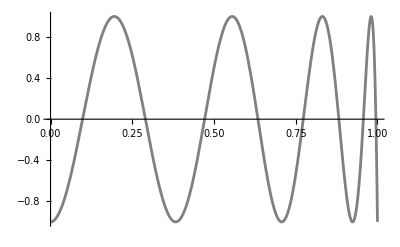

```mathematica
Plot [ 1-2(1-2(1-2(1-2x^2)^2)^2)^2,{x,0,1}, PlotStyle->Gray]
```

2) Построить график поверхности:

```mathematica
Plot3D[z = Sin[x/(y+Pi/10)], {x,0,2Pi}, {y,0,Pi/2},ColorFunction->"TemperatureMap", PlotPoints->40, AxesLabel->{"X", "Y", "Z"}]
```

-Graphics3D-

3) Решить уравнения относительно переменной x:

```mathematica
Solve [Log[x+Sqrt[x^2+a]]==b,x]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{x→1/2 ⅇ^-b (-a+ⅇ^(2 b))}}

```mathematica
Solve [x^4-5x^2-3==0, x]
```

{{x→-ⅈ √(1/2 (-5+√37))},{x→ⅈ √(1/2 (-5+√37))},{x→-√(1/2 (5+√37))},{x→√(1/2 (5+√37))}}

```mathematica
Solve [Cos[x]==Tan[x], x]
```

{{x→ConditionalExpression[π-ArcTan[√(1/2 (-1+√5))]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[√(1/2 (-1+√5))]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[-ⅈ √(1/2 (1+√5)),1/2 (-1-√5)]+2 π C[1], C[1]∈ℤ]},{x→ConditionalExpression[ArcTan[ⅈ √(1/2 (1+√5)),1/2 (-1-√5)]+2 π C[1], C[1]∈ℤ]}}

```mathematica
Solve[Log[Sqrt[x]]==Sqrt[Log[x]],x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1},{x→ⅇ^4}}

```mathematica
Solve[x^3-3x-1==0, x]
```

{{x→},{x→},{x→}}

```mathematica
Solve[a x^4+b x^3+1==0, x]
```

{{x→-b/(4 a)+1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))-1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)-b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)+1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))+1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)-b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)-1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))-1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)+b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))},{x→-b/(4 a)-1/2 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))+1/2 √(b^2/(2 a^2)-(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))-((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a)+b^3/(4 a^3 √(b^2/(4 a^2)+(4 (2/3)^(1/3))/((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))+((9 b^2+√3 √(-256 a^3+27 b^4))^(1/3))/(2^(1/3) 3^(2/3) a))))}}

4) Найти численное решение уравнения

```mathematica
NSolve[x^7+7x==7, x]
```

{{x→-1.3217-0.706695 ⅈ},{x→-1.3217+0.706695 ⅈ},{x→-0.137797-1.43289 ⅈ},{x→-0.137797+1.43289 ⅈ},{x→0.920191},{x→0.999402-0.797172 ⅈ},{x→0.999402+0.797172 ⅈ}}

```mathematica
NSolve[Cos[x]==x, x]
```

{{x→0.739085},{x→-2.48689+1.80936 ⅈ},{x→-9.10999+2.95017 ⅈ},{x→-15.488+3.45661 ⅈ},{x→-21.819+3.79031 ⅈ},{x→-28.1316+4.03995 ⅈ},{x→-34.435+4.23954 ⅈ},{x→-40.7329+4.40585 ⅈ},{x→-47.0274+4.54842 ⅈ},{x→-53.3196+4.67319 ⅈ},{x→-59.6102+4.78411 ⅈ},{x→-65.8995+4.88396 ⅈ},{x→-72.1878+4.97474 ⅈ},{x→-78.4754+5.05797 ⅈ},{x→-84.7625+5.1348 ⅈ},{x→-91.0491+5.20615 ⅈ}}

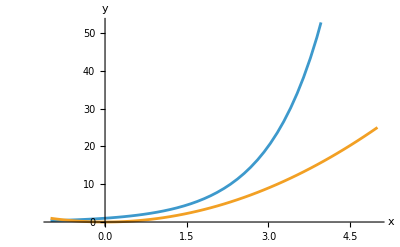

```mathematica
Plot[{Exp[x],x^2},{x,-1,5},AxesLabel->{"x","y"}]
```

```mathematica
FindRoot[Exp[x]==x^2,{x,-0.7}]
```

{x→-0.703467}

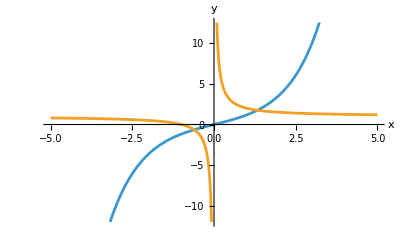

```mathematica
Plot[{Sinh[x],1+1/x},{x,-5,5},AxesLabel->{"x","y"}]
```

```mathematica
FindRoot[Sinh[x]==1+1/x,{x,-0.6}]
```

{x→-0.607635}

```mathematica
FindRoot[Sinh[x]==1+1/x,{x,1.3}]
```

{x→1.32752}

```mathematica
ContourPlot[Evaluate[{Re[Sin[u+I v]-(1-(u+I v)/2)]==0,Im[Sin[u+I v]-(1-(u+I v)/2)]==0}],{u,-10,10},{v,-10,10},ContourStyle->{Red, Blue}]
```

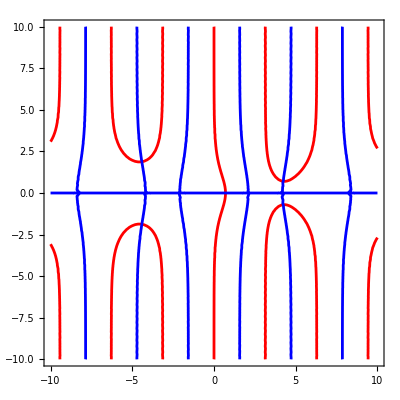

```mathematica
ContourPlot[Evaluate[{Re[Exp[u+I v]-(u+I v+1)]==0,Im[Exp[u+I v]-(u+I v+1)]==0}],{u,-10,10},{v,-10,10},ContourStyle->{Red, Blue}]
```

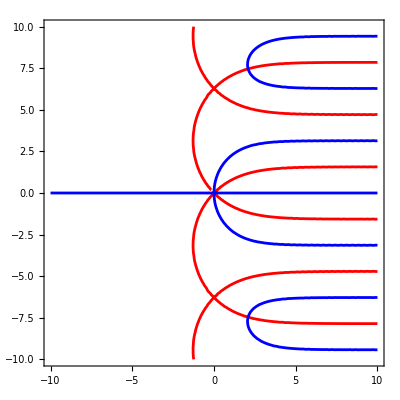

5) Решить системы уравнений:

```mathematica
Solve[{x+y==5,x-y==1},{x,y}]
```

{{x→3,y→2}}

```mathematica
{x+y==5,x-y==1}/. Solve[{x+y==5,x-y==1},{x,y}]
```

{{True,True}}

```mathematica
Solve[{Sqrt[x+y]==Sqrt[x y],x^2+y^2==1},{x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→1/2 (1-√2+√(-1+2 √2)),y→1/2 (1-√2-√(-1+2 √2))},{x→1/2 (1-√2-√(-1+2 √2)),y→1/2 (1-√2+√(-1+2 √2))},{x→1/2+1/(√2)+1/2 ⅈ √(1+2 √2),y→1/2+1/(√2)-1/2 ⅈ √(1+2 √2)},{x→1/2+1/(√2)-1/2 ⅈ √(1+2 √2),y→1/2+1/(√2)+1/2 ⅈ √(1+2 √2)}}

```mathematica
Solve[{Sin[x+y]==Cos[x-y],Tan[x y]==Cos[x y]},{x,y}]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→(4 ArcCos[-√(1/2 (-1+√5))])/π,y→π/4},{x→(4 ArcCos[√(1/2 (-1+√5))])/π,y→π/4},{x→(4 ArcCos[-ⅈ √(1/2 (1+√5))])/(3 π),y→-(3 π)/4},{x→(4 ArcCos[ⅈ √(1/2 (1+√5))])/(3 π),y→-(3 π)/4},{x→π/4,y→(4 ArcCos[-√(1/2 (-1+√5))])/π},{x→π/4,y→(4 ArcCos[√(1/2 (-1+√5))])/π},{x→-(3 π)/4,y→(4 ArcCos[-ⅈ √(1/2 (1+√5))])/(3 π)},{x→-(3 π)/4,y→(4 ArcCos[ⅈ √(1/2 (1+√5))])/(3 π)}}

6) Найти численное решение системы

```mathematica
Clear[x,y,z]
```

```mathematica
NSolve[{x^2+y^2-z^2==1,x+y==z,Sinh[z]==x^2+y^2},{x,y,z}]
```

{{x→-0.36031+0.29384 ⅈ,y→0.833413+0.679666 ⅈ,z→0.473104+0.973506 ⅈ},{x→5.28335+8.24171 ⅈ,y→-0.0275635+0.0429974 ⅈ,z→5.25579+8.2847 ⅈ},{x→0.0530998+0.0556156 ⅈ,y→-4.49033+4.70307 ⅈ,z→-4.43723+4.75869 ⅈ},{x→-5.83816+11.5994 ⅈ,y→0.0173105+0.034393 ⅈ,z→-5.82085+11.6338 ⅈ},{x→-0.0275635+0.0429974 ⅈ,y→5.28335+8.24171 ⅈ,z→5.25579+8.2847 ⅈ},{x→-0.36031-0.29384 ⅈ,y→0.833413-0.679666 ⅈ,z→0.473104-0.973506 ⅈ},{x→5.28335-8.24171 ⅈ,y→-0.0275635-0.0429974 ⅈ,z→5.25579-8.2847 ⅈ},{x→3.15411,y→-0.158523,z→2.99559},{x→0.0173105+0.034393 ⅈ,y→-5.83816+11.5994 ⅈ,z→-5.82085+11.6338 ⅈ},{x→-4.49033+4.70307 ⅈ,y→0.0530998+0.0556156 ⅈ,z→-4.43723+4.75869 ⅈ},{x→-4.49033-4.70307 ⅈ,y→0.0530998-0.0556156 ⅈ,z→-4.43723-4.75869 ⅈ},{x→-0.0275635-0.0429974 ⅈ,y→5.28335-8.24171 ⅈ,z→5.25579-8.2847 ⅈ},{x→-0.158523,y→3.15411,z→2.99559},{x→0.833413+0.679666 ⅈ,y→-0.36031+0.29384 ⅈ,z→0.473104+0.973506 ⅈ},{x→0.833413-0.679666 ⅈ,y→-0.36031-0.29384 ⅈ,z→0.473104-0.973506 ⅈ},{x→0.0530998-0.0556156 ⅈ,y→-4.49033-4.70307 ⅈ,z→-4.43723-4.75869 ⅈ}}

7) Решить дифференциальное уравнение

```mathematica
DSolve[x^2 y''[x]+5 x y'[x]+y[x]==0,y[x],x]
```

{{y[x]→x^(1/2 (-4-2 √3)) C[1]+x^(1/2 (-4+2 √3)) C[2]}}

```mathematica
DSolve[x^2 y''[x]+3 x y'[x]+y[x]==Sin[2 x],y[x],x]
```

{{y[x]→C[1]/x-CosIntegral[2 x]/(2 x)+(C[2] Log[x])/x}}

```mathematica
DSolve[{x^2 y''[x]+5 x y'[x]+y[x]==x^(-2+Sqrt[3]),y[1]==-1/12,y'[1]==(2+Sqrt[3])/12},y[x],x]
```

{{y[x]→1/12 x^(-2+√3) (-1+2 √3 Log[x])}}

```mathematica
DSolve[y''[x]+y[x]/Sin[x]^2==0,y[x],x]
```

{{y[x]→C[1] (-1+Cos[x]^2)^(1/4) LegendreP[-1/2,(ⅈ √3)/2,Cos[x]]+C[2] (-1+Cos[x]^2)^(1/4) LegendreQ[-1/2,(ⅈ √3)/2,Cos[x]]}}

8) Решить систему аналиически

```mathematica
DSolve[{y''[t]==4 x[t]-5 y[t],x''[t]==4 y[t]-5 x[t],y[0]==1,x[0]==0,y'[0]==0,x'[0]==1},{x,y},t]
```

{{x→Function[{t},1/6 (3 Cos[t]-3 Cos[3 t]+3 Sin[t]+Sin[3 t])],y→Function[{t},1/6 (3 Cos[t]+3 Cos[3 t]+3 Sin[t]-Sin[3 t])]}}

```mathematica
Clear[x,y,t]

DSolve[{x''[t]==t^2+y[t],y'[t]==x[t]},{x,y},t]
```

{{x→Function[{t},1/3 ⅇ^(-t/2) C[1] (ⅇ^(3 t/2)+2 Cos[(√3 t)/2])+1/3 ⅇ^(-t/2) C[3] (ⅇ^(3 t/2)-Cos[(√3 t)/2]-√3 Sin[(√3 t)/2])+1/3 ⅇ^(-t/2) C[2] (ⅇ^(3 t/2)-Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])-1/9 ⅇ^(-3 t/2) (ⅇ^(3 t/2)-Cos[(√3 t)/2]-√3 Sin[(√3 t)/2]) (2+2 t+t^2+2 ⅇ^(3 t/2) (-1-t+t^2) Cos[(√3 t)/2]-2 √3 ⅇ^(3 t/2) (-1+t) Sin[(√3 t)/2])+1/9 ⅇ^(-3 t/2) (ⅇ^(3 t/2)-Cos[(√3 t)/2]+√3 Sin[(√3 t)/2]) (-2-2 t-t^2+ⅇ^(3 t/2) (-4+2 t+t^2) Cos[(√3 t)/2]+√3 ⅇ^(3 t/2) (-2+t) t Sin[(√3 t)/2])-1/9 ⅇ^(-3 t/2) (ⅇ^(3 t/2)+2 Cos[(√3 t)/2]) (2+2 t+t^2-ⅇ^(3 t/2) (2-4 t+t^2) Cos[(√3 t)/2]+√3 ⅇ^(3 t/2) (-2+t^2) Sin[(√3 t)/2])],y→Function[{t},1/3 ⅇ^(-t/2) C[3] (ⅇ^(3 t/2)+2 Cos[(√3 t)/2])+1/3 ⅇ^(-t/2) C[2] (ⅇ^(3 t/2)-Cos[(√3 t)/2]-√3 Sin[(√3 t)/2])+1/3 ⅇ^(-t/2) C[1] (ⅇ^(3 t/2)-Cos[(√3 t)/2]+√3 Sin[(√3 t)/2])-1/9 ⅇ^(-3 t/2) (ⅇ^(3 t/2)+2 Cos[(√3 t)/2]) (2+2 t+t^2+2 ⅇ^(3 t/2) (-1-t+t^2) Cos[(√3 t)/2]-2 √3 ⅇ^(3 t/2) (-1+t) Sin[(√3 t)/2])+1/9 ⅇ^(-3 t/2) (ⅇ^(3 t/2)-Cos[(√3 t)/2]-√3 Sin[(√3 t)/2]) (-2-2 t-t^2+ⅇ^(3 t/2) (-4+2 t+t^2) Cos[(√3 t)/2]+√3 ⅇ^(3 t/2) (-2+t) t Sin[(√3 t)/2])-1/9 ⅇ^(-3 t/2) (ⅇ^(3 t/2)-Cos[(√3 t)/2]+√3 Sin[(√3 t)/2]) (2+2 t+t^2-ⅇ^(3 t/2) (2-4 t+t^2) Cos[(√3 t)/2]+√3 ⅇ^(3 t/2) (-2+t^2) Sin[(√3 t)/2])]}}

9) Решить уравнение, построить график решения

```mathematica
sol=NDSolve[{x''[t]==-Sin[x[t]],x[0]==0,x'[0]==1.999},x,{t,0,20}]
```

{{x→InterpolatingFunction[…]}}

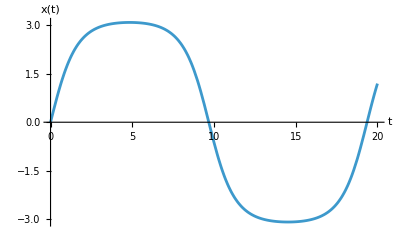

```mathematica
Plot[Evaluate[x[t]/. sol],{t,0,20},AxesLabel->{"t","x(t)"}]
```

# Лаба 3

1) а) Доказать тождество: (1+2+...+n)^2 = 1^3+2^3+...+n^3

```mathematica
Simplify[Sum[i,{i,1,n}]^2-Sum[i^3,{i,1,n}]]
```

0

б) Вычислить сумму Sum[k/(k^4 + k^2 + 1), {k, 1, n}]

```mathematica
Sum[k/(k^4+k^2+1),{k,1,n}]
```

1/2-1/(2 (1+n+n^2))

2) Вычислить Sum[i^k, {i, 0, n}]

```mathematica
Sum[i^k,{i,0,n}]
```

0^k+HarmonicNumber[n,-k]

3) Сколькими нулями заканчивается 10000! Количество нулей равно количеству множителей 5 в разложении факториала

```mathematica
IntegerExponent[10000!,5]
```

2499

4) Определить количество простых чисел среди первой тысячи чисел Фибоначчи

```mathematica
Count[PrimeQ[Fibonacci[Range[1000]]],True]
```

21

5) Написать программу, находящую все совершенные числа до 1000

```mathematica
Select[Range[1000],DivisorSigma[1,#]==2 #&]
```

{6,28,496}

6) Доказать, что среднее арифметическое двух неотрицательных чисел не меньше среднего геометрического

```mathematica
Simplify[(a+b)/2>=Sqrt[a*b],Assumptions->{a>=0,b>=0}]
```

True

7) Найти минимум функции Exp[x] + 1.2/x на интервале x от 1 до 2

```mathematica
FindMinimum[Exp[x]+1.2/x,{x,1,2}]
```

{3.71698,{x→0.752098}}